# Structural Decompositions

Partial Differential Equations (PDEs) and the matrices that represent them frequently have distinct pieces.  Matrices sometimes have blocs that are nice.  Matrices sometimes have patterns and structures that can be exploited.

## Artificial Example

Here is a very artificial example!  I think it makes a point! Remember A0 here has a blindingly fast FFT based solver.

```mathematica
n=223;
A0=SparseArray[{Band[{1,1}]->2.0,Band[{1,2}]->-1.0,Band[{2,1}]->-1.0},{n,n}];
A=A0;A⟦23,43⟧=1.2;A⟦123,43⟧=17.2;A⟦23,143⟧=-1.2;A⟦23,3⟧=51.2;A⟦3,43⟧=-11.2;
M=Inverse[A0];
TabView[{
"λ(A_0)"->ListPlot[ReIm[Eigenvalues[A0]],PlotRange->All],
"λ(A)"->ListPlot[ReIm[Eigenvalues[A]],PlotRange->All],
"λ(M.A)"->ListPlot[ReIm[Eigenvalues[M.A]],PlotRange->All],
"λ(A.M)"->ListPlot[ReIm[Eigenvalues[A.M]],PlotRange->All]
}]
```

Eigenvalues::arh: Because finding 223 out of the 223 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvalues.

1234

```mathematica
ReIm[Eigenvalues[M.A]]⟦1;;12⟧
```

{{229.24,115.176},{229.24,-115.176},{1.,0.},{1.,2.13509×10^-14},{1.,-2.13509×10^-14},{1.,0.},{1.,5.68061×10^-15},{1.,-5.68061×10^-15},{1.,1.03377×10^-14},{1.,-1.03377×10^-14},{1.,2.03356×10^-15},{1.,-2.03356×10^-15}}

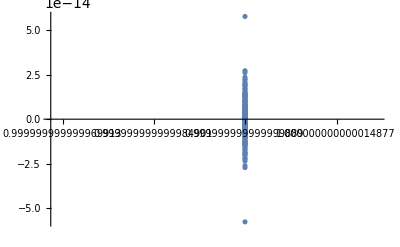

```mathematica
ListPlot[ReIm[Eigenvalues[M.A]]⟦12;;-1⟧,PlotRange->All]
```

```mathematica
Norm[Inverse[A]-M,"Frobenius"]/Norm[Inverse[A]]
```

3.30554

## Less Artificial Example

Suppose we want to solve 
	u_t+u u_x=u_xx  with periodic boundary conditions u(0)=u(L)
This is called the viscous Burgers equation https://en.wikipedia.org/wiki/Burgers%27_equation and has a solution for all time t under reasonable conditions.  It is the simplest nonlinear model for wave breaking.  The first thing we should do is the linear simplification 
	u_t+α u_x=u_xx with periodic boundary conditions u(0)=u(L)
This is a 1D advection diffusion equation.  See the wiki page
https://en.wikipedia.org/wiki/Convection%E2%80%93diffusion_equation
for more discussion.

We have not talked about PDEs at all but we are going to do the simplest possible thing with the time variable and try the approximation 
	u_t≈(u(t+Δt,x)-u(t,x))/Δt.
As before we will think of a vector of values u in the x direction.